```mathematica
Manipulate[
Module[{δx,δy,δw,δh},
δx=1;δy=0.4*δx;δw=0.35*δx;δh=0.5*δy;

Column[{
Graphics[{
{EdgeForm@Thick,FaceForm@GrayLevel@0.95,Rectangle[{0,0},{δx,δy}]},
Thick,Line[{{#,-0.75*δy},{#,1.75*δy}}]&/@{0,δx},

{Blue,Arrow[{{0.25*δx,0},{0.25*δx,-δh}}],Dashed,Arrow[{{0.25*δx,δy+δh},{0.25*δx,0}}]},
{Green,Arrow[{{0.75*δx,δy},{0.75*δx,δy+δh}}],Dashed,Arrow[{{0.75*δx,-δh},{0.75*δx,δy}}]},

Arrowheads@0.09,Thickness@0.025,Arrow@BezierCurve[pt],Red,PointSize@0.013,Point@pt
},ImageSize->{600,400},AspectRatio->Full,PlotRange->{{-δw,δx},{-δh,δy+δh}},PlotRangePadding->{{None,0.01},Scaled@0.1}],
pt}]
],
(*Control[{{pt,{{0,0.2},{0.42,0.2},{0.84,0.15},{0.83,0.3},{0.83,0.4}}},Locator,Appearance->None}]*)
Control[{{pt,{{0,0.2},{0.42,0.2},{0.89,0.14},{0.83,0.3},{0.83,0.4}}},Locator,Appearance->None}]
]
```

```mathematica
0.14/0.4
```

0.35

## FEED TO VAPOR

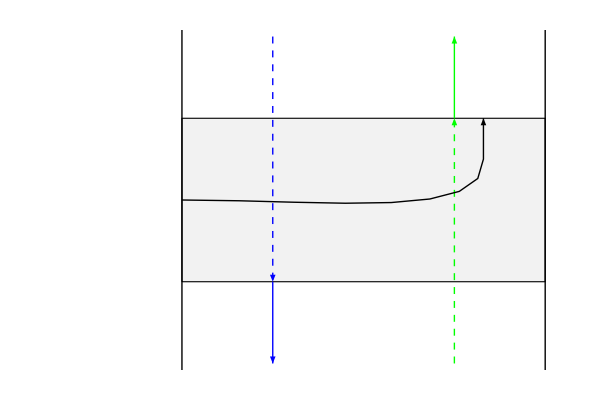

```mathematica
Module[{δx,δy,δw,δh,pt},
δx=1;δy=0.4*δx;δw=0.35*δx;δh=0.5*δy;
pt={{0,δy/2},{0.42*δx,δy/2},{0.84*δx,0.375*δy},{0.83*δx,0.75*δy},{0.83*δx,δy}};

Graphics[{
{EdgeForm@Thick,FaceForm@GrayLevel@0.95,Rectangle[{0,0},{δx,δy}]},
Thick,Line[{{#,-0.75*δy},{#,1.75*δy}}]&/@{0,δx},

{Blue,Arrow[{{0.25*δx,0},{0.25*δx,-δh}}],Dashed,Arrow[{{0.25*δx,δy+δh},{0.25*δx,0}}]},
{Green,Arrow[{{0.75*δx,δy},{0.75*δx,δy+δh}}],Dashed,Arrow[{{0.75*δx,-δh},{0.75*δx,δy}}]},

(*{Arrow@BezierCurve[#],Red,PointSize@0.015,Point@#}&@{{0,δy/2},{0.83*δx,0.5*δy},{0.83*δx,δy}}*)
Arrow@BezierCurve[pt],
},ImageSize->{600,400},AspectRatio->Full,PlotRange->{{-δw,δx},{-δh,δy+δh}},PlotRangePadding->{{None,0.01},Scaled@0.1}]
]
```

```mathematica
Module[{δx,δy,data},
δx=1;δy=0.4*δx;
data={{0,0.2},{0.42,0.2},{0.84,0.15},{0.83,0.3},{0.83,0.4}};

{{0,δy/2},{0.42*δx,δy/2},{0.84*δx,0.375*δy},{0.83*δx,0.75*δy},{0.83*δx,δy}}==data
]
```

True